# 共形（保角）映射

### Reference

Conformal map between square and diskhttps://www.johndcook.com/blog/2022/11/28/conformal-square-disk/Nonehttps://www.johndcook.com/blog/2022/11/28/conformal-square-disk/HyperlinkActionRecycledHyperlinkActive

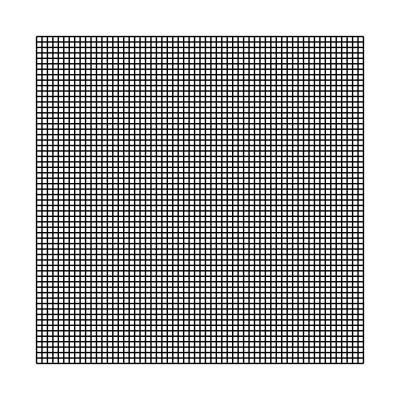

```mathematica
r=1.5;
s=0.05;
pts=Table[{x,y},{x,-r,r,s},{y,-r,r,s}];
grid=Line/@{pts,ptsᵀ};
Graphics[{grid}]
```

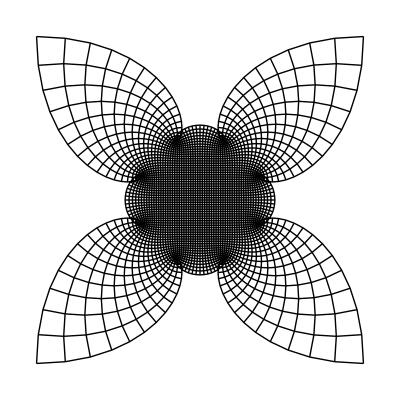

```mathematica
f[z_]:=z+0.0731647z+0.00358709 z^9
pts2=Map[ReIm@f[Complex@@#]&,pts,{2}];
grid2=Line/@{pts2,pts2ᵀ};
Graphics[{grid2}]
```

```mathematica
draw[pts_]:=Graphics[{Line/@{pts,ptsᵀ}}]
```

```mathematica
genPts[r_,s_]:=Table[{x,y},{x,-r,r,s},{y,-r,r,s}]
```

```mathematica
transfer[f_,pts_]:=Map[ReIm@f[Complex@@#]&,pts,{2}]
```

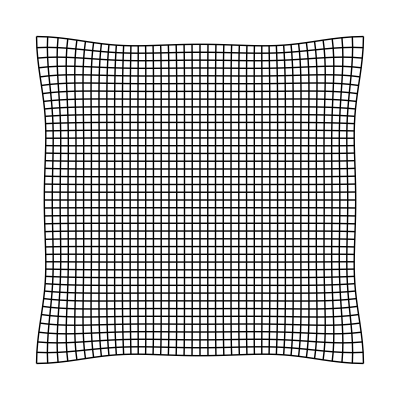

```mathematica
draw[transfer[f,genPts[1.,0.05]]]
```

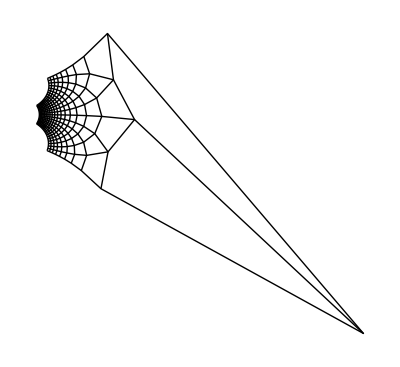

```mathematica
s2d[z_]:=(1-I)/2 JacobiSD[(1+I)/2 EllipticK[z],1/2]
draw@transfer[s2d,genPts[1.,0.11]]
```

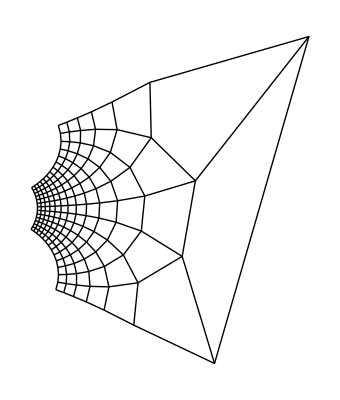

```mathematica
%//draw
```

```mathematica
EllipticK
```

```mathematica
JacobiSD
```

```mathematica
pts3=Map[ReIm@f[Complex@@CoordinateTransform["Cartesian"->"Polar" ,#]]&,pts,{2}];
grid3=;
Graphics[{grid3}]
```

ArcTan::indet: 碰到不定表达式 ArcTan[0.,0.].

-Graphics-

```mathematica
PolarPlot[]
```

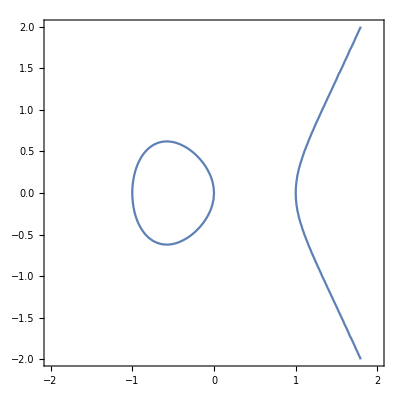

```mathematica
ContourPlot[y^2==x^3-x,{x,-2,2},{y,-2,2},Axes->True]
```

```mathematica
包络线
```